```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* take a renormalization path (seq), a site label (i) and an approximant size (n) and return the new renormalization path, the new site label and the new size after one renormalization group operation *)
ClearAll[i,n];
iterSeq[{seq_,i_,n_}]:=Block[{inew=i,seqn=seq,nnew=n},
If[i>Fibonacci[n-1],seqn="m"<>seq;inew=i-Fibonacci[n-1];nnew=n-2;,
If[i>Fibonacci[n-2],seqn="a"<>seq;inew=i-Fibonacci[n-2];nnew=n-3,
seqn="m"<>seq;nnew=n-2;]];
{seqn,inew,nnew}
]
```

```mathematica
(* false when n<3 *)
test=#[[3]]≥3&;
(* variant where we forget about the site number *)
path2[i_,n_]:=NestWhile[iterSeq,{"",i,n},test][[1]]
```

```mathematica
(* Display all the paths for a system size *)
paths[n_]:=path2[#,n]&/@Range[Fibonacci[n]]
```

```mathematica
(* compute intensity numerically, at finite ρ *)
ρ=0.1;
n=13;
{val,vec}=Eigensystem[hp[13,ρ,1.]];
o=Ordering[val];
val=val[[o]];
vec=vec[[o]];
int=Abs[vec]^2;

(* generate the list of positions where the intensity is nonzero at zero order *)
p=paths[n+2];
(* at first order there is intensity only at positions whose renormalization path matches the one of the corresponding energy level *)
m=Table[Flatten[Position[p,p[[a]]]],{a,Fibonacci[n+2]}];
```

```mathematica
(* evaluate λ numerically *)
lamb=Table[Total@int[[a,m[[a]]]],{a,Length@int}];
```

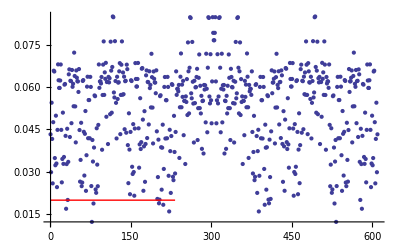

```mathematica
ListPlot[1-lamb,PlotRange->All,Epilog->{Thick,Red,Line[{{0,2 ρ^2},{Fibonacci[n],2 ρ^2}}]}]
```